# Calculations in paper (Fourier Space)

## Zero order solutions

```mathematica
U0=1;g=0.5;
U[t_]=U0 JacobiCD[g t U0,-1];
```

## First order wave solutions

```mathematica
(*Solutions for Λ,Φ,λ*)
```

```mathematica
eqns={Λ''[t]+2 I g p λ[t]U[t]+2 g^2 U[t]^2(2Φ[t]+Λ[t])==0,Φ''[t]+p^2 Φ[t]+2 I g p λ[t]U[t]+2 g^2 U[t]^2(2Φ[t]+Λ[t])==0,λ''[t]+p^2 λ[t]-I g p(2Φ[t]+Λ[t])U[t]+2 g^2 U[t]^2 λ[t]==0};
ibc={Λ[0]==0.01,Λ'[0]==0,λ[0]==.01,λ'[0]==0,Φ[0]==.01,Φ'[0]==0};
```

```mathematica
sol=ParametricNDSolve[{eqns,ibc},{Λ,λ,Φ},{t,0,200},p]
```

{Λ→ParametricFunction[<>],λ→ParametricFunction[<>],Φ→ParametricFunction[<>]}

```mathematica
Φ[p_,t_]=Φ[p][t]/.sol;
```

```mathematica
Λ[p_,t_]=Λ[p][t]/.sol;
```

```mathematica
λ[p_,t_]=λ[p][t]/.sol;
```

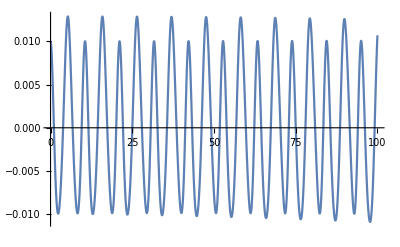

```mathematica
Plot[Re[Φ[1,t]],{t,0,100},PlotLegends->"Expressions"]
```

```mathematica
Plot[{Re[Φ[0,t]],Re[Φ[0.05,t]],Re[Φ[3,t]]},{t,0,100},PlotLegends->"Expressions"]
```

$Aborted

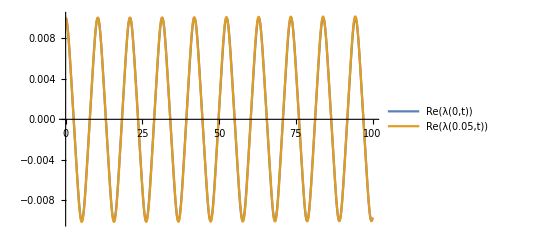

```mathematica
Plot[{Re[λ[0,t]],Re[λ[0.05,t]]},{t,0,100},PlotLegends->"Expressions"]
```

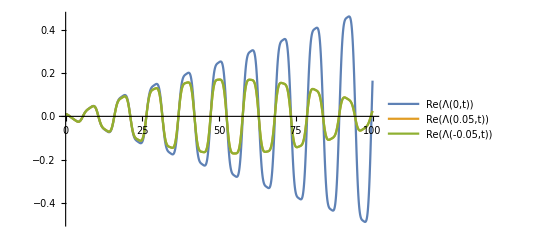

```mathematica
Plot[{Re[Λ[0,t]],Re[Λ[0.05,t]],Re[Λ[-0.05,t]]},{t,0,100},PlotLegends->"Expressions"]
```

```mathematica
(*Solutions for ϕ1,ϕ2,η1,η2 *)
```

```mathematica
s={{1,0,0},{0,1,0}};n={0,0,1};
```

```mathematica
eab=Table[Sum[Normal[LeviCivitaTensor[3]][[i]][[k]][[m]]s[[a]][[i]] n[[k]]s[[b]][[m]],{i,1,3},{k,1,3},{m,1,3}],{a,1,2},{b,1,2}]
```

{{0,-1},{1,0}}

```mathematica
eqns1={Subscript[ϕ, 1]''[t]+p^2/2 Subscript[ϕ, 1][t]+p^2/2 Subscript[η, 2][t]-I g p U[t]Subscript[ϕ, 2][t]==0,Subscript[ϕ, 2]''[t]+p^2/2 Subscript[ϕ, 2][t]-p^2/2 Subscript[η, 1][t]+I g p U[t]Subscript[ϕ, 1][t]==0,Subscript[η, 1]''[t]+p^2/2 Subscript[η, 1][t]-p^2/2 Subscript[ϕ, 2][t]+I g p U[t]Subscript[η, 2][t]+2 g^2 U[t]^2 Subscript[η, 1][t]==0,Subscript[η, 2]''[t]+p^2/2 Subscript[η, 2][t]+p^2/2 Subscript[ϕ, 1][t]-I g p U[t]Subscript[η, 1][t]+2 g^2 U[t]^2 Subscript[η, 2][t]==0};
ibc1={Subscript[ϕ, 1][0]==.01,Subscript[ϕ, 1]'[0]==0,Subscript[ϕ, 2][0]==.01,Subscript[ϕ, 2]'[0]==0,Subscript[η, 1][0]==.01,Subscript[η, 1]'[0]==0,Subscript[η, 2][0]==.01,Subscript[η, 2]'[0]==0};
```

```mathematica
sol1=ParametricNDSolve[{eqns1,ibc1},{Subscript[ϕ, 1],Subscript[ϕ, 2],Subscript[η, 1],Subscript[η, 2]},{t,0,200},p]
```

{ϕ_1→ParametricFunction[<>],ϕ_2→ParametricFunction[<>],η_1→ParametricFunction[<>],η_2→ParametricFunction[<>]}

```mathematica
ϕ1[p_,t_]=Subscript[ϕ, 1][p][t]/.sol1;
```

```mathematica
ϕ2[p_,t_]=Subscript[ϕ, 2][p][t]/.sol1;
```

```mathematica
η1[p_,t_]=Subscript[η, 1][p][t]/.sol1;
```

```mathematica
η2[p_,t_]=Subscript[η, 2][p][t]/.sol1;
```

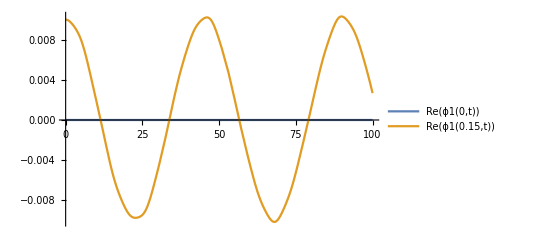

```mathematica
Plot[{Re[ϕ1[0,t]],Re[ϕ1[0.15,t]]},{t,0,100},PlotLegends->"Expressions"]
```

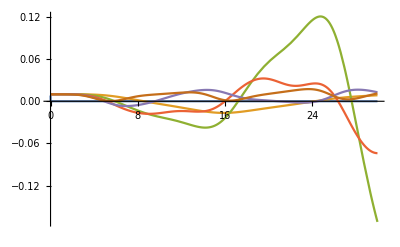

```mathematica
Plot[Evaluate[Table[Re[ϕ2[p,t]],{p,0,1,0.2}]],{t,0,30},PlotRange->All]
```

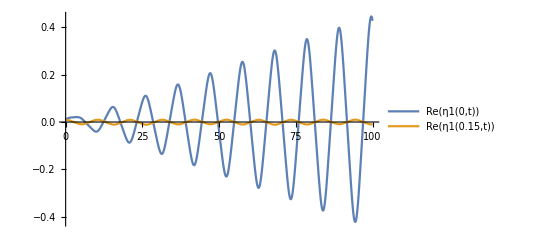

```mathematica
Plot[{Re[η1[0,t]],Re[η1[0.15,t]]},{t,0,100},PlotLegends->"Expressions",PlotRange->All]
```

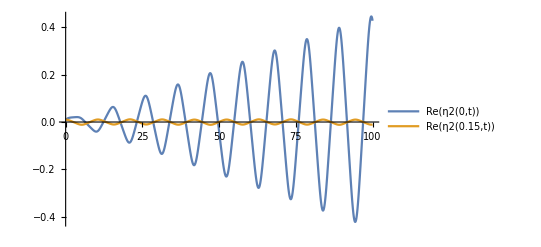

```mathematica
Plot[{Re[η2[0,t]],Re[η2[0.15,t]]},{t,0,100},PlotLegends->"Expressions",PlotRange->All]
```

```mathematica
(*Solutions for Subscript[ψ, 1],Subscript[ψ, 2]*)
```

```mathematica
Qaik={{{1,0,0},{0,-1,0},{0,0,0}},{{0,1,0},{1,0,0},{0,0,0}}};
```

```mathematica
Qab=Table[Sum[Normal[LeviCivitaTensor[3]][[i]][[j]][[k]]Qaik[[a]][[i]][[l]]n[[j]]Qaik[[b]][[k]][[l]],{l,1,3},{i,1,3},{j,1,3},{k,1,3}],{a,1,2},{b,1,2}]
```

{{0,-2},{2,0}}

```mathematica
eqns2={Subscript[ψ, 1]''[t]+p^2 Subscript[ψ, 1][t]-2I g p U[t]Subscript[ψ, 2][t]==0,Subscript[ψ, 2]''[t]+p^2 Subscript[ψ, 2][t]+2I g p U[t]Subscript[ψ, 1][t]==0};
ibc2={Subscript[ψ, 1][0]==0.01,Subscript[ψ, 1]'[0]==0,Subscript[ψ, 2][0]==0.01,Subscript[ψ, 2]'[0]==0};
```

```mathematica
sol2=ParametricNDSolve[{eqns2,ibc2},{Subscript[ψ, 1],Subscript[ψ, 2]},{t,0,200},p]
```

{ψ_1→ParametricFunction[<>],ψ_2→ParametricFunction[<>]}

```mathematica
ψ1[p_,t_]=Subscript[ψ, 1][p][t]/.sol2;
```

```mathematica
ψ2[p_,t_]=Subscript[ψ, 2][p][t]/.sol2;
```

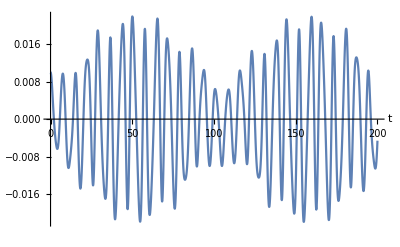

```mathematica
Plot[Re[ψ1[0.9,t]],{t,0,200},AxesLabel->Automatic]
```

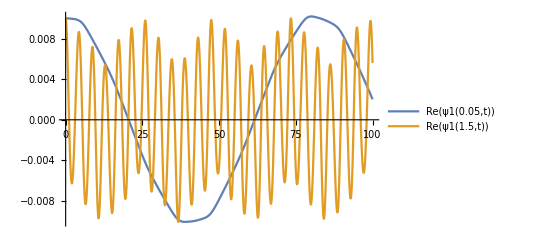

```mathematica
Plot[{Re[ψ1[0.05,t]],Re[ψ1[1.5,t]]},{t,0,100},PlotLegends->"Expressions",PlotRange->All]
```

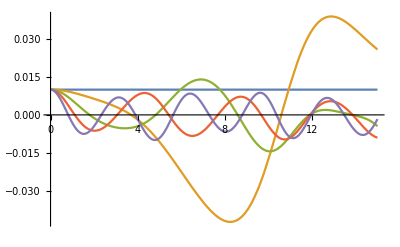

```mathematica
Plot[Evaluate[Table[Re[ψ1[p,t]],{p,0,2,0.5}]],{t,0,15},PlotRange->All]
```

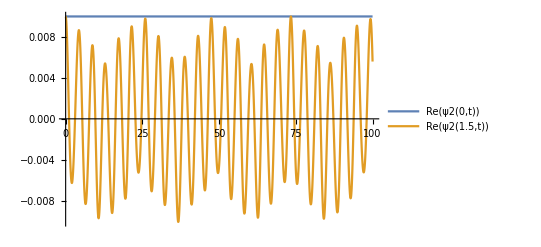

```mathematica
Plot[{Re[ψ2[0,t]],Re[ψ2[1.5,t]]},{t,0,100},PlotLegends->"Expressions",PlotRange->All]
```

```mathematica
(*Converting momentum space to normal space using ψ(t,z)=1/(2π)(∫_-Inf)^Inf dpⅇ^ipz ψ(t,p)*)
```

```mathematica
R[m_,k_]:=Root[HermiteH[m,#]&,k]
```

```mathematica
m=20;
```

```mathematica
zi=Table[R[m,i]//N,{i,1,m}];
```

```mathematica
zi
```

{-5.38748,-4.60368,-3.94476,-3.34785,-2.78881,-2.25497,-1.73854,-1.23408,-0.737474,-0.245341,0.245341,0.737474,1.23408,1.73854,2.25497,2.78881,3.34785,3.94476,4.60368,5.38748}

```mathematica
wi=Table[(2^(m-1)Factorial[m] √π)/(m^2(HermiteH[m-1,zi[[i]]])^2),{i,1,m}]
```

{2.22939×10^-13,4.39934×10^-10,1.08607×10^-7,7.80256×10^-6,0.000228339,0.00324377,0.0248105,0.109017,0.286676,0.462244,0.462244,0.286676,0.109017,0.0248105,0.00324377,0.000228339,7.80256×10^-6,1.08607×10^-7,4.39934×10^-10,2.22939×10^-13}

```mathematica
f[p_,t_,z_]=Exp[p(p+I z)]ψ1[p,t];
```

```mathematica
psi11[t_,z_]=Sum[wi[[i]]f[p,t,z]/.p->zi[[i]],{i,1,m}];
```

```mathematica
(*Comparing with actual ψ function*)
```

```mathematica
Plot3D[{Re[psi11[t,z]],psi1[t,z]},{t,0,15},{z,-10,10},PlotRange->All,PlotLegends->"Expressions"]
```

-Graphics3D-

At small times, the functions are almost same. At larger times, there is a divergent behaviour because of numerical differentiation approximations.

```mathematica
gg[p_,t_,z_]=Exp[p(p+I z)]ψ2[p,t];
```

```mathematica
psi22[t_,z_]=Sum[wi[[i]]gg[p,t,z]/.p->zi[[i]],{i,1,m}];
```

```mathematica
(*Comparing with actual ψ function*)
```

```mathematica
Plot3D[{Re[psi22[t,z]],psi2[t,z]},{t,0,15},{z,-10,10},PlotRange->All,PlotLegends->"Expressions"]
```

-Graphics3D-

```mathematica
(*Error*)
```

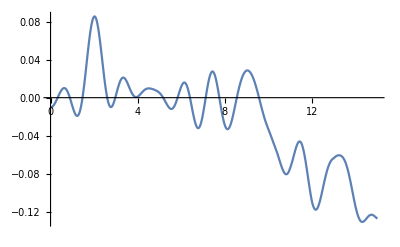

```mathematica
Plot[Re[psi22[t,2]]-psi2[t,2],{t,0,15}]
```

Error is small at smaller times and large at larger times.

```mathematica
met={{-1,0,0,0},{0,1+k hpp,hc,0},{0,hc,1-k hpp,0},{0,0,0,1}};MatrixForm[met]
```

(-1 | 0 | 0 | 0
0 | 1+hpp k | hc | 0
0 | hc | 1-hpp k | 0
0 | 0 | 0 | 1)

```mathematica
Det[met]
```

-1+hc^2+hpp^2 k^2

## Second order solutions

```mathematica
Clear[u];
eqns3={u''[t]+2 g^2 u[t]^3+g^2/6 u[t](Sum[4η1[p,t]Conjugate[η1[p,t]]+4η2[p,t]Conjugate[η2[p,t]]+4λ[p,t]Conjugate[λ[p,t]]+8Φ[p,t]Conjugate[Φ[p,t]]+2Λ[p,t]Conjugate[Λ[p,t]]+4Φ[p,t]Conjugate[Λ[p,t]],{p,0,5}])+I g/12 Sum[p(2λ[p,t]Conjugate[Λ[p,t]]-2Λ[p,t]Conjugate[λ[p,t]]+4λ[p,t]Conjugate[Φ[p,t]]-4Φ[p,t]Conjugate[λ[p,t]]+4ψ1[p,t]Conjugate[ψ2[p,t]]-4ψ2[p,t]Conjugate[ψ1[p,t]]+2ϕ1[p,t]Conjugate[ϕ2[p,t]]-2ϕ2[p,t]Conjugate[ϕ1[p,t]]-2η1[p,t]Conjugate[η2[p,t]]+2η2[p,t]Conjugate[η1[p,t]]),{p,0,5}]==0};
ibc3={u[0]==1,u'[0]==0};
```

```mathematica
sol3=NDSolve[{eqns3,ibc3},u,{t,0,200},MaxStepSize->0.01]
```

NDSolve::ndsz: At t == 157.615, step size is effectively zero; singularity or stiff system suspected.

{{u→InterpolatingFunction[{{0., 157.615}}, <>]}}

```mathematica
us[t_]=u[t]/.sol3;
```

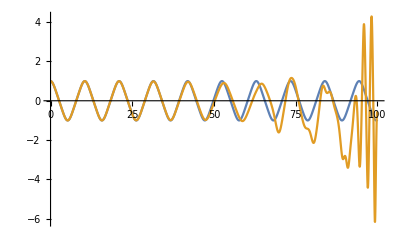

```mathematica
Plot[{U[t],Re[us[t]]},{t,0,100},PlotRange->All](*for p=15*)
```

```mathematica
resu[t_]=us''[t]+2 g^2 us[t]^3+g^2/6 us[t](Sum[4η1[p,t]Conjugate[η1[p,t]]+4η2[p,t]Conjugate[η2[p,t]]+4λ[p,t]Conjugate[λ[p,t]]+8Φ[p,t]Conjugate[Φ[p,t]]+2Λ[p,t]Conjugate[Λ[p,t]]+4Φ[p,t]Conjugate[Λ[p,t]],{p,0,5}])+I g/12 Sum[p(2λ[p,t]Conjugate[Λ[p,t]]-2Λ[p,t]Conjugate[λ[p,t]]+4λ[p,t]Conjugate[Φ[p,t]]-4Φ[p,t]Conjugate[λ[p,t]]+4ψ1[p,t]Conjugate[ψ2[p,t]]-4ψ2[p,t]Conjugate[ψ1[p,t]]+2ϕ1[p,t]Conjugate[ϕ2[p,t]]-2ϕ2[p,t]Conjugate[ϕ1[p,t]]-2η1[p,t]Conjugate[η2[p,t]]+2η2[p,t]Conjugate[η1[p,t]]),{p,0,5}];
```

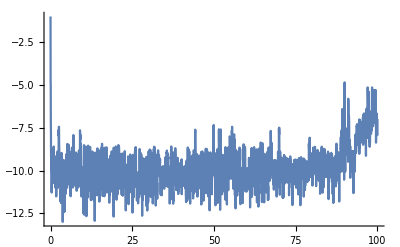

```mathematica
Plot[RealExponent[resu[t]],{t,0,100},PlotRange->All]
```

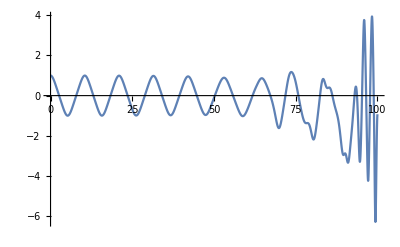

```mathematica
Plot[Re[u[t]],{t,0,100},PlotRange->All](*for p=10*)
```

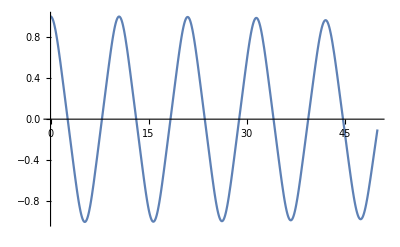

```mathematica
Plot[Re[u[t]]/.sol3,{t,0,50},PlotRange->All](*for p=5*)
```

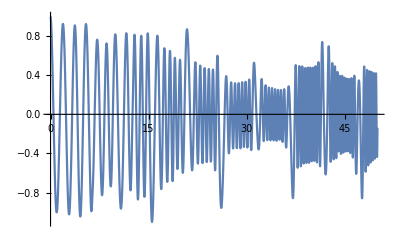

```mathematica
Plot[Re[u[t]]/.sol3,{t,0,50},PlotRange->All](*for p=15*)
```

## Hamiltonian

```mathematica
(*For condensate*)
```

```mathematica
Hu[t_]=3/2(us'[t]us'[t]+g^2 us[t]^4);
```

```mathematica
Hu0[t_]=3/2(U'[t]U'[t]+g^2 U[t]^4);
```

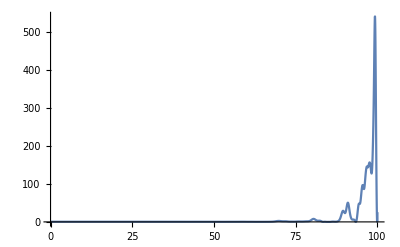

```mathematica
Plot[Re[Hu[t]],{t,0,100},PlotRange->Full]
```

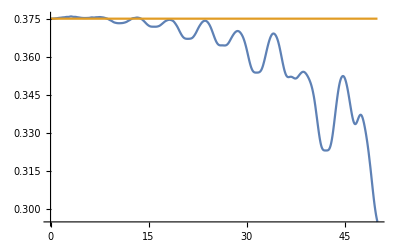

```mathematica
Plot[{Re[Hu[t]],Hu0[t]},{t,0,50},PlotRange->Full]
```

```mathematica
(*For particles:*)
```

```mathematica
Hp[t_]=1/2 Sum[D[ψ1[p,t],t]Conjugate[D[ψ1[p,t],t]]+D[ψ2[p,t],t]Conjugate[D[ψ2[p,t],t]]+D[ϕ1[p,t],t]Conjugate[D[ϕ1[p,t],t]]+D[ϕ2[p,t],t]Conjugate[D[ϕ2[p,t],t]]+1/2 D[Λ[p,t],t]Conjugate[D[Λ[p,t],t]]+D[η1[p,t],t]Conjugate[D[η1[p,t],t]]+D[η2[p,t],t]Conjugate[D[η2[p,t],t]]+D[λ[p,t],t]Conjugate[D[λ[p,t],t]]+p^2(ψ1[p,t]Conjugate[ψ1[p,t]]+ψ2[p,t]Conjugate[ψ2[p,t]])+p^2/2(ϕ1[p,t]Conjugate[ϕ1[p,t]]+ϕ2[p,t]Conjugate[ϕ2[p,t]])+p^2 Φ[p,t]Conjugate[Φ[p,t]]+p^2/2(η1[p,t]Conjugate[η1[p,t]]+η2[p,t]Conjugate[η2[p,t]])+p^2 λ[p,t]Conjugate[λ[p,t]]+p^2/2(η2[p,t]Conjugate[ϕ1[p,t]]+ϕ1[p,t]Conjugate[η2[p,t]]-η1[p,t]Conjugate[ϕ2[p,t]]-ϕ2[p,t]Conjugate[η1[p,t]]),{p,0,5}];
```

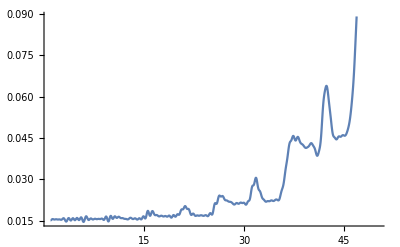

```mathematica
Plot[Re[Hp[t]],{t,1,50}]
```

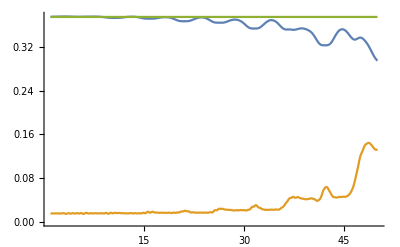

```mathematica
Plot[{Re[Hu[t]],Re[Hp[t]],Hu0[t]},{t,1,50}]
```

```mathematica
Hu00=Hu0[0]
```

0.375

```mathematica
(*for interaction:*)
```

```mathematica
Hint[t_]=1/2 Sum[I g p us[t](η2[p,t]Conjugate[η1[p,t]]-η1[p,t]Conjugate[η2[p,t]])+2 I g p us[t](ψ1[p,t]Conjugate[ψ2[p,t]]-ψ2[p,t]Conjugate[ψ1[p,t]])+I g p us[t](ϕ1[p,t]Conjugate[ϕ2[p,t]]-ϕ2[p,t]Conjugate[ϕ1[p,t]])-I g p us[t](2Φ[p,t]Conjugate[λ[p,t]]-2λ[p,t]Conjugate[Φ[p,t]]+Λ[p,t]Conjugate[λ[p,t]]-λ[p,t]Conjugate[Λ[p,t]])+2 g^2 us[t]^2(η1[p,t]Conjugate[η1[p,t]]+η2[p,t]Conjugate[η2[p,t]])+2 g^2 us[t]^2 λ[p,t]Conjugate[λ[p,t]]+g^2 us[t]^2(4Φ[p,t]Conjugate[Φ[p,t]]+2Φ[p,t]Conjugate[Λ[p,t]]+2Λ[p,t]Conjugate[Φ[p,t]]+Λ[p,t]Conjugate[Λ[p,t]]),{p,0,5}];
```

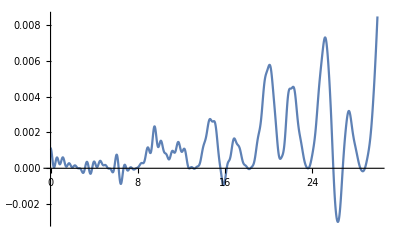

```mathematica
Plot[Re[Hint[t]],{t,0,30}]
```

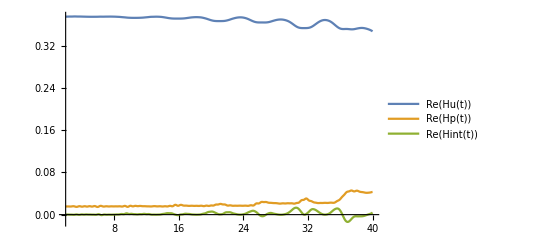

```mathematica
Plot[{Re[Hu[t]],Re[Hp[t]],Re[Hint[t]]},{t,2,40},PlotLegends->"Expressions",PlotRange->Full]
```

```mathematica
Ht[t_]=Hu[t]+Hp[t]+Hint[t];
```

```mathematica
Ht[0]
```

General::munfl: -2.6986×10^-6 (1.37317×10^9-2.1403×10^-304 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -2.6986×10^-6 (-1.37317×10^9+2.14031×10^-304 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -2.6986×10^-6 (1.37317×10^9-2.1403×10^-304 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.392625+0. ⅈ}

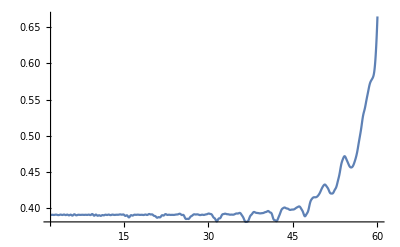

```mathematica
Plot[Re[Ht[t]],{t,2,60},PlotRange->All]
```

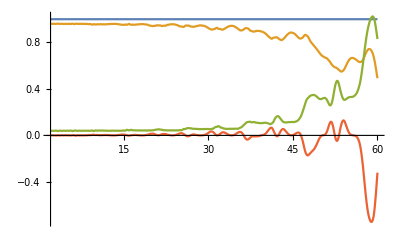

```mathematica
Plot[{Re[Ht[t]]/Re[Ht[t]],Re[Hu[t]]/Re[Ht[t]],Re[Hp[t]]/Re[Ht[t]],Re[Hint[t]]/Re[Ht[t]]},{t,2,60},PlotRange->All]
```

```mathematica
Ht[59]
```

{0.577802-0.000159558 ⅈ}

```mathematica
Hp[59]
```

0.589097-6.77626×10^-21 ⅈ

## Others:

```mathematica
-------------------------------------------------------(*Rough:*)------------------------------------------------------------
```

```mathematica
4η1[p,t]Conjugate[η1[p,t]]+4η2[p,t]Conjugate[η2[p,t]]+2Λ[p,t]Conjugate[Λ[p,t]]+4Φ[p,t]Conjugate[Λ[p,t]]+4λ[p,t]Conjugate[λ[p,t]]+8Φ[p,t]Conjugate[Φ[p,t]];
2λ[p,t]Conjugate[Λ[p,t]]-2Λ[p,t]Conjugate[λ[p,t]]-2η1[p,t]Conjugate[η2[p,t]]+2η2[p,t]Conjugate[η1[p,t]]+4λ[p,t]Conjugate[Φ[p,t]]-4Φ[p,t]Conjugate[λ[p,t]]+2ϕ1[p,t]Conjugate[ϕ2[p,t]]-2ϕ2[p,t]Conjugate[ϕ1[p,t]];
```

```mathematica
Clear[u];
eqns4={u''[t]+2 g^2 u[t]^3+I g/12 Sum[p(4ψ1[p,t]Conjugate[ψ2[p,t]]-4ψ2[p,t]Conjugate[ψ1[p,t]]),{p,0,10}]==0};
ibc4={u[0]==1,u'[0]==0};
```

```mathematica
sol4=NDSolve[{eqns4,ibc4},u,{t,0,50}]
```

{{u→InterpolatingFunction[…]}}

```mathematica
ur[t_]=u[t]/.sol4;
```

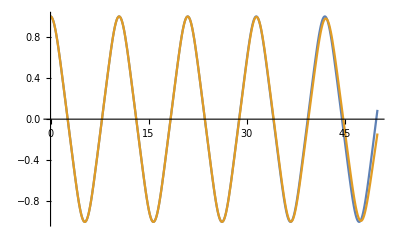

```mathematica
Plot[{U[t],ur[t]},{t,0,50}]
```

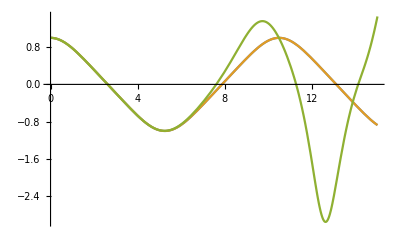

```mathematica
Plot[{ur[t],U[t],us[t]},{t,0,15}]
```

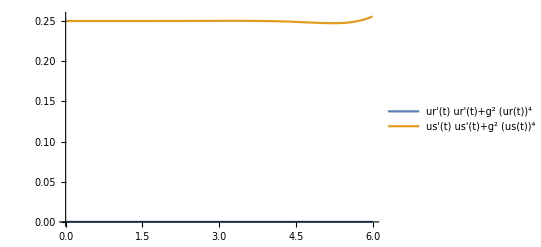

```mathematica
Plot[{(ur'[t]ur'[t]+g^2 ur[t]^4),(us'[t]us'[t]+g^2 us[t]^4)},{t,0,6},PlotLegends->"Expressions"]
```

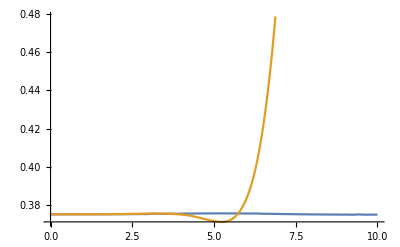

```mathematica
Plot[{3/2(ur'[t]ur'[t]+g^2 ur[t]^4),Hu[t]},{t,0,10}]
```

Conclusion: Even with the only psi1 and psi2 modes, we have the same behaviour for energy density (Hu(t)). It means the transverse modes are also responsible for energy swap effect.